# Test computation method for EWPT

Isaac R Wang

This code tests different computation methods for the EWPT strength.
Since the model is SM with small Higgs at high energy scale, an arbitrarily light Higgs and a lighter smaller top Yukawa coupling is applied here. Slightly smaller gauge couplings are also applied.
Main refs: hep-ph/9203203, hep-ph/9212235, 2205.08815

## The 1-loop perturbation theory in 3d

Ref: the DRalgo package (arXiv:2205.08815)

### Preparison

```mathematica
SetDirectory[NotebookDirectory[]];
$LoadGroupMath=True;
<<DRalgo`
```

-Graphics- | DRDRDRDRDRDRDRDRDRDRDRDRDRDR DRalgo DRDRDRDRDRDRDRDRDRDRDRDRDRDRDVersion: 1.01 beta (16-05-2022)Authors: Andreas Ekstedt, Philipp Schicho, Tuomas V.I. TenkanenReference: 2205.08815 [hep-ph]Repository link: https://github.com/DR-algo/DRalgoDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRD

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.2 (6/May/2020)Author: Renato FonsecaReference: 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[blocks_] is Protected.

GroupMath is an independent package, and is not part of DRalgo

Please Cite GroupMath: Comput.Phys.Commun. 267 (2021) 108085 • e-Print: 2011.01764 [hep-th]

```mathematica
Group={"SU3","SU2","U1"};
RepAdjoint={{1,1},{2},0};
HiggsDoublet={{{0,0},{1},1/2},"C"};
RepScalar={HiggsDoublet};
CouplingName={g3,g2,g1};
Rep1={{{1,0},{1},1/6},"L"}; (*qL*)
Rep2={{{1,0},{0},2/3},"R"}; (*uR*)
Rep3={{{1,0},{0},-1/3},"R"}; (*dR*)
Rep4={{{0,0},{1},-1/2},"L"}; (*lL*)
Rep5={{{0,0},{0},-1},"R"}; (*eR*)
RepFermion1Gen={Rep1,Rep2,Rep3,Rep4,Rep5};
RepFermion3Gen={RepFermion1Gen}//Flatten[#,1]&;
{gvvv,gvff,gvss,λ1,λ3,λ4,μij,μIJ,μIJC,Ysff,YsffC}=AllocateTensors[Group,RepAdjoint,CouplingName,RepFermion3Gen,RepScalar];
InputInv={{1,1},{True,False}};
MassTerm1=CreateInvariant[Group,RepScalar,InputInv][[1]];
Vmass=-μsq MassTerm1;
μij=GradMass[Vmass];
Vquartic=λ MassTerm1^2;
λ4=GradQuartic[Vquartic];
InputInv={{1,1,2},{False,False,True}};
YukawaDoublet1=CreateInvariantYukawa[Group,RepScalar,RepFermion3Gen,InputInv][[1]]//Simplify;
Ysff=-GradYukawa[yt1*YukawaDoublet1];
YsffC=Simplify[Ysff//Normal//Conjugate,Assumptions->{yt1>0}]//SparseArray;
ImportModelDRalgo[Group,gvvv,gvff,gvss,λ1,λ3,λ4,μij,μIJ,μIJC,Ysff,YsffC,Verbose->False];
(*Import model.*)
PosFermion=PrintFermionRepPositions[];
FermionMat=Table[{nF,i},{i,PosFermion}];
DefineNF[FermionMat]
PerformDRhard[](*Compute thermal masses, effective couplings, beta functions and anomalous dimensions*)
PerformDRsoft[{}](*Integrate out heavy temporal scalar*)
```

```mathematica
DefineNewTensorsUS[μij,λ4,λ3,gvss,gvvv];
ϕvev={0,0,0,ϕ}//SparseArray;
DefineVEVS[ϕvev];
MassMatrix=PrintTensorsVEV[];VectorMass=MassMatrix[[2]]//Normal;VectorEigenvectors=FullSimplify[Transpose[Normalize/@Eigenvectors[VectorMass[[11;;12,11;;12]]]],Assumptions->{g1>0,g2>0,ϕ>0}];
DVRot={{IdentityMatrix[10],0},{0,VectorEigenvectors}}//ArrayFlatten;DSRot=IdentityMatrix[4];RotateTensorsUSPostVEV[DSRot,DVRot];
CalculatePotentialUS[](*Run this to compute the potential*)
```

The Vector Mass-Matrix is not Diagonal

(1) Scalar Mass, (2) Vector Mass, (3) Scalar Quartic, (4) Scalar Cubic, (5) VSS, (6) VVS, (7) VVV

```mathematica
BetaFunctions4D[];
sub1={g1->√g1sq[Λ],g2->√g2sq[Λ],g3->√g3sq[Λ],λ->λh[Λ],μsq->μhsq[Λ],yt1->yt[Λ]};
βg1sq=g1^2/.BetaFunctions4D[]/.sub1;
βg2sq=g2^2/.BetaFunctions4D[]/.sub1;
βg3sq=g3^2/.BetaFunctions4D[]/.sub1;
βλ=λ/.BetaFunctions4D[]/.sub1//Expand;
βμsq=μsq/.BetaFunctions4D[]/.sub1//Expand;
βyt=yt1/.BetaFunctions4D[]/.sub1//Expand;
```

```mathematica
solveBetas[{g1sqInit_,g2sqInit_,g3sqInit_,ytInit_,μhsqInit_,λhInit_}]:=Block[{initialScale,Λ,nF,g1sq,g2sq,g3sq,yt,λh,μhsq,eqg1sq,eqg2sq,eqg3sq,eqyt,eqλh,eqμhsq},
nF=3;
eqg1sq=βg1sq;
eqg2sq=βg2sq;
eqg3sq=βg3sq;
eqyt=βyt;
eqλh=βλ;
eqμhsq=βμsq;
initialScale= 83.;
{g1sq,g2sq,g3sq,yt,μhsq,λh}=NDSolveValue[{
(*Beta functions*)
Λ D[g1sq[Λ],Λ]==eqg1sq,
Λ D[g2sq[Λ],Λ]==eqg2sq,
Λ D[g3sq[Λ],Λ]==eqg3sq,
Λ D[yt[Λ],Λ]==eqyt,
Λ D[λh[Λ],Λ]==eqλh,
Λ D[μhsq[Λ],Λ]==eqμhsq,
(*initial condition*)
g1sq[initialScale]==g1sqInit,
g2sq[initialScale]==g2sqInit,
g3sq[initialScale]==g3sqInit,
yt[initialScale]==ytInit,
λh[initialScale]==λhInit,
μhsq[initialScale]==μhsqInit
},
{g1sq,g2sq,g3sq,yt,μhsq,λh},
{Λ,5,5000}
];
Return[{g1sq,g2sq,g3sq,yt,μhsq,λh}];
]
```

```mathematica
Parameters[Temp_,scale_,g1sq_,g2sq_,g3sq_,yt_,μhsq_,λh_]:=
(*The input is the temperature, the RG-scale, and running 4d parameters.*)
Block[{nF,g1,g1sq3d,g2,g2sq3d,g3,g3sq3d,λh3d,mhsqLO,mhsqNLO,mhsq3d,Lb,Lf,numbers,gaugeDR,μhsq3d,mDsqU1,mDsqSU2,mDsqSU3,DebyemassRule,λhUS,g1sq3dUS,g2sq3dUS,g3sq3dUS,msqUSLO,msqUSNLO,μhsq3dUS},
(*Numbers. This should be applied later*)
numbers={g1->√g1sq,g2->√g2sq,g3->√g3sq,yt1->yt,μsq->μhsq,λ->λh,nF->3,μ->scale,T->Temp};

(*From 4d to 3d*)
g1sq3d=g13d^2/.PrintCouplings[]/.PrintConstants[]/.numbers;
g2sq3d=g23d^2/.PrintCouplings[]/.PrintConstants[]/.numbers;
g3sq3d=g33d^2/.PrintCouplings[]/.PrintConstants[]/.numbers;
gaugeDR={g13d->√g1sq3d,g23d->√g2sq3d,g33d->√g3sq3d};
λh3d=λ3d/.PrintCouplings[]/.PrintConstants[]/.numbers;
mhsqLO=μsq3d/.PrintScalarMass["LO"]/.PrintConstants[]/.numbers;
mhsqNLO=μsq3d/.PrintScalarMass["NLO"]/.PrintTemporalScalarCouplings[]/.{g13d->√g1sq3d,g23d->√g2sq3d,g33d->√g3sq3d,λ3d->λh3d}/.PrintConstants[]/.numbers;
μhsq3d=mhsqLO+mhsqNLO;

(*From 3d to 3d ultra soft*)
(*First get the debye masses*)
mDsqU1=(μsqU1/.PrintDebyeMass["LO"]/.PrintConstants[]/.numbers)+(μsqU1/.PrintDebyeMass["NLO"]/.PrintConstants[]/.numbers);
mDsqSU2=(μsqSU2/.PrintDebyeMass["LO"]/.PrintConstants[]/.numbers)+(μsqSU2/.PrintDebyeMass["NLO"]/.PrintConstants[]/.PrintConstants[]/.numbers);
mDsqSU3=(μsqSU3/.PrintDebyeMass["LO"]/.PrintConstants[]/.numbers)+(μsqSU3/.PrintDebyeMass["NLO"]/.PrintConstants[]/.numbers);
DebyemassRule={μsqSU3->mDsqSU3,μsqSU2->mDsqSU2,μsqU1->mDsqU1};

(*Then printout the couplings*)
λhUS=λ3dUS/.PrintCouplingsUS[]/.DebyemassRule/.PrintTemporalScalarCouplings[]/.gaugeDR/.PrintConstants[]/.{λ3d->λh3d}/.numbers;
g1sq3dUS=g13dUS^2/.PrintCouplingsUS[]/.gaugeDR/.DebyemassRule/.PrintConstants[]/.numbers;
g2sq3dUS=g23dUS^2/.PrintCouplingsUS[]/.gaugeDR/.DebyemassRule/.PrintConstants[]/.numbers;
g3sq3dUS=g33dUS^2/.PrintCouplingsUS[]/.PrintConstants[]/.gaugeDR/.DebyemassRule/.numbers;
msqUSLO=μsq3dUS/.PrintScalarMassUS["LO"]/.{μsq3d->μhsq3d}/.PrintTemporalScalarCouplings[]/.PrintConstants[]/.DebyemassRule/.gaugeDR/.{λ3d->λh3d}/.numbers;
msqUSNLO=μsq3dUS/.PrintScalarMassUS["NLO"]/.{μsq3d->μhsq3d}/.PrintTemporalScalarCouplings[]/.PrintConstants[]/.DebyemassRule/.gaugeDR/.{λ3d->λh3d}/.numbers;
μhsq3dUS=(msqUSLO+msqUSNLO)/.{μsq3d->μhsq3d};
Return[{g1sq3dUS,g2sq3dUS,g3sq3dUS,μhsq3dUS,λhUS}]
]
```

```mathematica
Veff3d[ϕvalue_,Temp_,g1sq3d_,g2sq3d_,g3sq3d_,μhsq3d_,λh3d_]:=Block[{g1,g2,g3,μ3,μsq,λ,coupling,scale,Veff,μ3US,nF,μsqSU3,msqSU3},
nF=3;
(*couplings and 3d RG scale.*)
coupling={g1->√g1sq3d,g2->√g2sq3d,g3->√g3sq3d,μsq->μhsq3d,λ->λh3d};
msqSU3=(μsqSU3/.PrintDebyeMass["LO"]/.coupling);
scale={μ3->g3sq3d,μ3US->√msqSU3};(*Use the Debye mass as the soft scale μ3US*)

Veff=(PrintEffectivePotential["LO"]+PrintEffectivePotential["NLO"](*+PrintEffectivePotential["NNLO"]*))/.{ϕ->ϕvalue}/.coupling/.scale/.{T->Temp};

Return[Veff]
]
```

```mathematica
findThermo[g1sq_,g2sq_,g3sq_,yt_,mh_,λ_,scaleFactor_]:=Block[{Tc,Tmax,Tmin,TT,Tm,Tp,Tloopmax,v1Limit,μhsq,g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit,scale,g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d,ϕ3,Veff,Veff0,Veffnorm,acc,scalingFactor,minSol,Tnext,Vc,ϕ0,ϕ3d,ϕc,ϕcTc,ϕ,Tupper},
Tmax=200;
Tmin=30;
Tloopmax=10;
v1Limit=10;
μhsq=mh^2/2;
{g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit}={g1sq,g2sq,g3sq,yt,μhsq,λ};
{g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue}=solveBetas[{g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit}];

Tupper=Catch[Do[
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>0,Throw[TT];];
,{TT,Tmin,Tmax,10}]];
Tm=Tupper-10;
Tp=Tupper;
TT=(Tm+Tp)/2;
(*Scan over temeperatures*)
Do[
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>0,
Tnext=(TT+Tm)/2//N;
Tp=TT;
TT=Tnext;];
If[Vc<0,
Tnext=(TT+Tp)/2//N;
Tm=TT;
TT=Tnext;];
If[Tloop==Tloopmax &&Vc>0,
(*In this case we cannot find the correct ϕc. Go back to the previous Tm.*)
Tc=Tm;
TT=Tc;
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
ϕcTc=ϕc/Tc;];
If[Tloop==Tloopmax &&Vc<0,
ϕc=Abs[ϕ]/.minSol[[2]];
Tc=TT//N;
ϕcTc=ϕc/Tc;];
,{Tloop,1,Tloopmax,1}
];
Print["Find critical temperature: ",Tc,", field value at vev: ",ϕc,", transition strength: ",ϕcTc," Veff at ϕc: ",Vc];
Return[{Tc,ϕc,ϕcTc}];
]
```

### Test parameters: input parameters for 1-loop

```mathematica
(*Parameter input and integral definition. Here we use a smaller gauge and Yukawa couplings to mimic the high-scale stuff*)
mW=73.;
mZ=83.;
mt=90.;
αsmZ=0.11;
g3mZ=√(4π αsmZ);
GF=1.1663787×10^-5;
v=(√2 GF)^(-1/2);
(*Define integrals. The scale is fixed to be mZ*)
A0[M_]:=M^2(1-Log[M^2/mZ^2]);
B0[p_,M1_,M2_]:=-NIntegrate[Log[(x M1^2+(1-x)M2^2-x(1-x)p^2)/mZ^2],{x,0,1}]
```

```mathematica
MSbar[mh_]:=Block[{λmZ,mhmZsq,ytmZ,g2mZ,g1mZ},
λmZ=GF/(√2)mh^2+1/((4π)^2 v^4)(3 mt^2(mh^2-4 mt^2)B0[mh,mt,mt]+3 mh^2 A0[mt]+1/4(mh^4-4 mh^2 mZ^2+12 mZ^4)B0[mh,mZ,mZ]+mh^2(7 mW^2-4 mZ^2)/(2(mZ^2-mW^2))A0[mZ]+1/2(mh^4-4 mh^2 mW^2+12 mW^4)B0[mh,mW,mW]-(3 mh^2 mW^2)/(2(mh^2-mW^2))A0[mh]+mh^2/2(-11+(3 mh^2)/(mh^2-mW^2)-(3 mW^2)/(mZ^2-mW^2))A0[mW]+9/4 mh^4 B0[mh,mh,mh]+1/4(mh^4+mh^2(mZ^2+2 mW^2-6 mt^2)-8(mZ^4+2 mW^4)))//Re;
mhmZsq=mh^2+1/((4π)^2 v^2)(6 mt^2(mh^2-4 mt^2)B0[mh,mt,mt]+24 mt^2 A0[mt]+(mh^4-4 mh^2 mW^2+12 mW^4)B0[mh,mW,mW]-2(mh^2+6 mW^2)A0[mW]+1/2(mh^4-4 mh^2 mZ^2+12 mZ^4)B0[mh,mZ,mZ]-(mh^2+6 mZ^2)A0[mZ]+9/2 mh^4 B0[mh,mh,mh]-3 mh^2 A0[mh])//Re;
ytmZ=2(GF/(√2)mt^2)^(1/2)+mt/(√2 v^3(4π)^2)(-(mh^2-4 mt^2)B0[mt,mh,mt]+(mt^2(80 mW^2 mZ^2-64 mW^4-7 mZ^4)+40 mW^2 mZ^4-32 mW^4 mZ^2-17 mZ^6)/(9 mt^2 mZ^2)B0[mt,mt,mZ]+(mt^2 mW^2+mt^4-2 mW^4)/mt^2 B0[mt,0,mW]+((3 mh^2)/(mh^2-mW^2)+2 mW^2/mt^2+3 mW^2/(mW^2-mZ^2)-10)A0[mW]+(3 mW^2/(mW^2-mh^2)+1)A0[mh]+(36 mt^2 mZ^2-56 mW^2 mZ^2+64 mW^4-17 mZ^4)/(9 mt^2 mZ^2)A0[mt]+((3 mW^2)/(mZ^2-mW^2)+(32 mW^4-40 mW^2 mZ^2+17 mZ^4)/(9 mt^2 mZ^2)-3)A0[mZ]+mh^2/2-3 mt^2-9 mW^2+7 mZ^2/18+64 mW^4/(9 mZ^2))+mt/(√2 v (4π))αsmZ(-8 A0[mt]/mt^2-8/3)//Re;
g2mZ=2(√2 GF)^(1/2)mW+2 mW/((4π)^2 v^3)((mh^4/(6 mW^2)-2 mh^2/3+2 mW^2)B0[mW,mh,mW]+(-mt^4/mW^2-mt^2+2 mW^2)B0[mW,0,mt]+1/6(-48 mW^4/mZ^2+mZ^4/mW^2-68 mW^2+16 mZ^2)B0[mW,mW,mZ]+1/6(mh^2(9/(mh^2-mW^2)+1/mW^2)+mZ^2/mW^2+mW^2(9/(mW^2-mZ^2)+48/mZ^2)-27)A0[mW]+(2-(mh^2(mh^2+8 mW^2))/(6 mW^2(mh^2-mW^2)))A0[mh]+(mt^2/mW^2+1)A0[mt]+1/6(24 mW^2/mZ^2-mZ^2/mW^2+9 mW^2/(mZ^2-mW^2)-17)A0[mW]+1/36(-3 mh^2+18 mt^2+288 mW^4/mZ^2-374 mW^2-3 mZ^2))//Re;
g1mZ=2(√2 GF)^(1/2)√(mZ^2-mW^2)+(2 √(mZ^2-mW^2))/((4π)^2 v^3)((88/9-(124 mW^2)/(9 mZ^2)+(mh^2+34 mW^2)/(6(mZ^2-mW^2)))A0[mZ]+(mh^2-4 mW^2)/(2(mh^2-mW^2))A0[mh]+(-7/9-mt^2/(mZ^2-mW^2)+64 mW^2/(9 mZ^2))A0[mt]+(mh^4+2 mW^2(mW^2-15 mZ^2)+3 mh^2(2 mW^2+7 mZ^2))/(6(mh^2-mW^2)(mW^2-mZ^2))A0[mW]-(mt^4+mW^2 mt^2-2 mW^4)/(mW^2-mZ^2)B0[mW,0,mt]-(mh^4-4 mZ^2 mh^2+12 mZ^4)/(6(mW^2-mZ^2))B0[mZ,mh,mZ]+(mh^4-4 mW^2 mh^2+12 mW^4)/(6(mW^2-mZ^2))B0[mW,mh,mW]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mW^2-mZ^2))B0[mW,mW,mZ]+1/9(-23 mW^2+7 mt^2+17 mZ^2-(64 mt^2 mW^2)/mZ^2-(9 mW^2(mt^2-mW^2))/(mZ^2-mW^2))B0[mZ,mt,mt]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mZ^2-mW^2))B0[mZ,mW,mW]+1/36(576 mW^4/mZ^2-242 mW^2-3 mh^2+257 mZ^2+36 mW^2/(mZ^2-mW^2)+mt^2(82-256 mW^2/mZ^2)))//Re;
Return[{λmZ,√mhmZsq,ytmZ,g2mZ,g1mZ}];
]
```

```mathematica
{λtest,mhtest,yttest,g2test,g1test}=MSbar[24.0];
findThermo[g1test^2,g2test^2,g3mZ^2,yttest,mhtest,λtest,1.0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.658188}. NIntegrate obtained -2.48037+1.07484 ⅈ and 0.000377172 for the integral and error estimates.

Find critical temperature: 54.0039, field value at vev: 106.07, transition strength: 1.96411 Veff at ϕc: -3.40111

{54.0039,106.07,1.96411}

```mathematica
TclistDR1loop={};
strengthlistDR1loop={};
Block[{scaleFactor,mhpole,Tc,ϕc,ϕcTc,λrun,mhrun,ytrun,g1run,g2run},
Do[
mhpole=mh;
Print["Higgs mass: ",mhpole," GeV."];
scaleFactor=1.0;
{λrun,mhrun,ytrun,g2run,g1run}=MSbar[mhpole];
{Tc,ϕc,ϕcTc}=findThermo[g1run^2,g2run^2,g3mZ^2,ytrun,mhrun,λrun,scaleFactor];
AppendTo[TclistDR1loop,{mhpole,Tc}];
AppendTo[strengthlistDR1loop,{mhpole,ϕcTc}];
,{mh,24,50,2}]]
```

Higgs mass: 24 GeV.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.658188}. NIntegrate obtained -2.48037+1.07484 ⅈ and 0.000377172 for the integral and error estimates.

Find critical temperature: 54.0039, field value at vev: 106.07, transition strength: 1.96411 Veff at ϕc: -3.40111

Higgs mass: 26 GeV.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.658188}. NIntegrate obtained -2.48037+1.07484 ⅈ and 0.000377172 for the integral and error estimates.

Find critical temperature: 57.6123, field value at vev: 98.0278, transition strength: 1.70151 Veff at ϕc: -3.38582

Higgs mass: 28 GeV.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.658188}. NIntegrate obtained -2.48037+1.07484 ⅈ and 0.000377172 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Find critical temperature: 61.2646, field value at vev: 90.8614, transition strength: 1.4831 Veff at ϕc: -0.375002

Higgs mass: 30 GeV.

Find critical temperature: 64.9414, field value at vev: 84.7871, transition strength: 1.30559 Veff at ϕc: -1.56659

Higgs mass: 32 GeV.

Find critical temperature: 68.6328, field value at vev: 80.1233, transition strength: 1.16742 Veff at ϕc: -12.3207

Higgs mass: 34 GeV.

Find critical temperature: 72.3193, field value at vev: 77.1666, transition strength: 1.06703 Veff at ϕc: -37.2172

Higgs mass: 36 GeV.

Find critical temperature: 75.9961, field value at vev: 74.9258, transition strength: 0.985917 Veff at ϕc: -63.1039

Higgs mass: 38 GeV.

Find critical temperature: 79.668, field value at vev: 73.3764, transition strength: 0.921028 Veff at ϕc: -92.4295

Higgs mass: 40 GeV.

Find critical temperature: 83.3398, field value at vev: 71.902, transition strength: 0.862756 Veff at ϕc: -116.579

Higgs mass: 42 GeV.

Find critical temperature: 87.085, field value at vev: 68.3377, transition strength: 0.784724 Veff at ϕc: -97.1702

Higgs mass: 44 GeV.

Find critical temperature: 90.8203, field value at vev: 64.7119, transition strength: 0.712526 Veff at ϕc: -75.2748

Higgs mass: 46 GeV.

Find critical temperature: 94.5508, field value at vev: 61.1579, transition strength: 0.646826 Veff at ϕc: -54.6419

Higgs mass: 48 GeV.

Find critical temperature: 98.2568, field value at vev: 58.1902, transition strength: 0.592226 Veff at ϕc: -41.5687

Higgs mass: 50 GeV.

Find critical temperature: 101.934, field value at vev: 55.365, transition strength: 0.543147 Veff at ϕc: -29.997

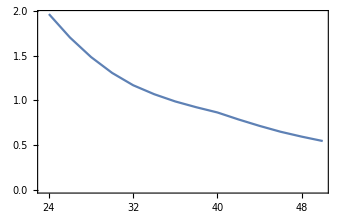

```mathematica
ListLinePlot[strengthlistDR1loop]
```

```mathematica
DRstrengthfunc[mh_]:=Interpolation[strengthlistDR][mh];
FindRoot[DRstrengthfunc[mh]==1.0,{mh,35}]
```

Interpolation::innd: First argument in strengthlistDR does not contain a list of data and coordinates.

FindRoot::nlnum: The function value {-1.+Interpolation[strengthlistDR][35.]} is not a list of numbers with dimensions {1} at {mh} = {35.}.

FindRoot[DRstrengthfunc(mh)==1.,{mh,35}]

## The 2-loop perturbation theory in 3d

```mathematica
Veff3d2loop[ϕvalue_,Temp_,g1sq3d_,g2sq3d_,g3sq3d_,μhsq3d_,λh3d_]:=Block[{g1,g2,g3,μ3,μsq,λ,coupling,scale,Veff,μ3US,nF,μsqSU3,msqSU3},
nF=3;
(*couplings and 3d RG scale.*)
coupling={g1->√g1sq3d,g2->√g2sq3d,g3->√g3sq3d,μsq->μhsq3d,λ->λh3d};
msqSU3=(μsqSU3/.PrintDebyeMass["LO"]/.coupling);
scale={μ3->g3sq3d,μ3US->√msqSU3};(*Use the Debye mass as the soft scale μ3US*)

Veff=(PrintEffectivePotential["LO"]+PrintEffectivePotential["NLO"]+PrintEffectivePotential["NNLO"])/.{ϕ->ϕvalue}/.coupling/.scale/.{T->Temp};

Return[Veff]
]
```

```mathematica
findThermo2loop[g1sq_,g2sq_,g3sq_,yt_,mh_,λ_,scaleFactor_]:=Block[{Tc,Tmax,Tmin,TT,Tm,Tp,Tloopmax,v1Limit,μhsq,g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit,scale,g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d,ϕ3,Veff,Veff0,Veffnorm,acc,scalingFactor,minSol,Tnext,Vc,ϕ0,ϕ3d,ϕc,ϕcTc,ϕ,Tupper},
Tmax=200;
Tmin=30;
Tloopmax=10;
v1Limit=10;
μhsq=mh^2/2;
{g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit}={g1sq,g2sq,g3sq,yt,μhsq,λ};
{g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue}=solveBetas[{g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit}];

Tupper=Catch[Do[
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d2loop[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>0,Throw[TT];];
,{TT,Tmin,Tmax,10}]];
Tm=Tupper-10;
Tp=Tupper;
TT=(Tm+Tp)/2;
(*Scan over temeperatures*)
Do[
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d2loop[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>0,
Tnext=(TT+Tm)/2//N;
Tp=TT;
TT=Tnext;];
If[Vc<0,
Tnext=(TT+Tp)/2//N;
Tm=TT;
TT=Tnext;];
If[Tloop==Tloopmax &&Vc>0,
(*In this case we cannot find the correct ϕc. Go back to the previous Tm.*)
Tc=Tm;
TT=Tc;
scale=scaleFactor*π*TT;
{ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ}={g1sqvalue[scale],g2sqvalue[scale],g3sqvalue[scale],ytvalue[scale],μsqvalue[scale],λhvalue[scale]};
{g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d}=Parameters[TT,scale,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ];
ϕ3d=ϕ/(√TT);
Veff=Veff3d2loop[ϕ3d,TT,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d]//Simplify;
ϕ0=10^-5;
Veff0=Veff/.{ϕ->ϕ0};
Veffnorm=(Veff-Veff0)//Re//Simplify;
acc=10;
minSol=NMinimize[{Veffnorm,ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
ϕcTc=ϕc/Tc;];
If[Tloop==Tloopmax &&Vc<0,
ϕc=Abs[ϕ]/.minSol[[2]];
Tc=TT//N;
ϕcTc=ϕc/Tc;];
,{Tloop,1,Tloopmax,1}
];
Print["Find critical temperature: ",Tc,", field value at vev: ",ϕc,", transition strength: ",ϕcTc," Veff at ϕc: ",Vc];
Return[{Tc,ϕc,ϕcTc}];
]
```

```mathematica
TclistDR2loop={};
strengthlistDR2loop={};
Block[{scaleFactor,mhpole,Tc,ϕc,ϕcTc,λrun,mhrun,ytrun,g1run,g2run},
Do[
mhpole=mh;
Print["Higgs mass: ",mhpole," GeV."];
scaleFactor=1.0;
{λrun,mhrun,ytrun,g2run,g1run}=MSbar[mhpole];
{Tc,ϕc,ϕcTc}=findThermo2loop[g1run^2,g2run^2,g3mZ^2,ytrun,mhrun,λrun,scaleFactor];
AppendTo[TclistDR2loop,{mhpole,Tc}];
AppendTo[strengthlistDR2loop,{mhpole,ϕcTc}];
,{mh,24,50,2}]]
```

Higgs mass: 24 GeV.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.658188}. NIntegrate obtained -2.48037+1.07484 ⅈ and 0.000377172 for the integral and error estimates.

Find critical temperature: 54.1162, field value at vev: 118.201, transition strength: 2.1842 Veff at ϕc: -2.80583

Higgs mass: 26 GeV.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.658188}. NIntegrate obtained -2.48037+1.07484 ⅈ and 0.000377172 for the integral and error estimates.

Find critical temperature: 57.6318, field value at vev: 110.832, transition strength: 1.92311 Veff at ϕc: -12.7702

Higgs mass: 28 GeV.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.658188}. NIntegrate obtained -2.48037+1.07484 ⅈ and 0.000377172 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Find critical temperature: 61.1914, field value at vev: 104.239, transition strength: 1.70349 Veff at ϕc: -11.1055

Higgs mass: 30 GeV.

Find critical temperature: 64.7852, field value at vev: 98.5371, transition strength: 1.52098 Veff at ϕc: -9.27492

Higgs mass: 32 GeV.

Find critical temperature: 68.3984, field value at vev: 93.5843, transition strength: 1.36822 Veff at ϕc: -7.11678

Higgs mass: 34 GeV.

Find critical temperature: 72.0264, field value at vev: 89.3118, transition strength: 1.23999 Veff at ϕc: -5.91953

Higgs mass: 36 GeV.

Find critical temperature: 75.6445, field value at vev: 85.7083, transition strength: 1.13304 Veff at ϕc: -7.63178

Higgs mass: 38 GeV.

Find critical temperature: 79.2725, field value at vev: 82.4926, transition strength: 1.04062 Veff at ϕc: -6.92513

Higgs mass: 40 GeV.

Find critical temperature: 82.8711, field value at vev: 80.0437, transition strength: 0.965882 Veff at ϕc: -14.4538

Higgs mass: 42 GeV.

Find critical temperature: 86.4453, field value at vev: 78.4098, transition strength: 0.907045 Veff at ϕc: -32.3356

Higgs mass: 44 GeV.

Find critical temperature: 90., field value at vev: 77.0931, transition strength: 0.85659 Veff at ϕc: -49.9115

Higgs mass: 46 GeV.

Find critical temperature: 93.5352, field value at vev: 75.9589, transition strength: 0.812089 Veff at ϕc: -64.1849

Higgs mass: 48 GeV.

Find critical temperature: 97.0313, field value at vev: 75.3662, transition strength: 0.77672 Veff at ϕc: -83.9222

Higgs mass: 50 GeV.

Find critical temperature: 100.508, field value at vev: 74.7396, transition strength: 0.74362 Veff at ϕc: -100.988

## The 1-loop perturbation theory in 4d

Here we use the on-shell renormalization scheme.

### 1-loop full form with resummation

```mathematica
Clear[mh,μ,λ]
```

```mathematica
μ[mh_]:=mh/(√2);
λ[mh_]:=μ[mh]^2/v^2;
B=3/(64 π^2 v^4)(2 mW^4+mZ^4-4 mt^4);
g=2 mW/v;
gY=√((4 mZ^2)/v^2-g^2);
V0[ϕ_,mh_]:=(-μ[mh]^2)/2 ϕ^2+λ[mh]/4 ϕ^4+2B v^2 ϕ^2-3/2 B ϕ^4+B ϕ^4 Log[ϕ^2/v^2];
JBFit[x_]:=-Sum[(+1)^(1+j)*(x/j^2)*BesselK[2,j*Sqrt[x]],{j,1,20}];
JFFit[x_]:=Sum[(-1)^(1+j)*(x/j^2)*BesselK[2,j*Sqrt[x]],{j,1,20}];
VFT[ϕ_,T_]:=T^4/(2 π^2)(6JBFit[(mW^2 ϕ^2)/(T^2 v^2)]+3JBFit[(mZ^2 ϕ^2)/(T^2 v^2)]-12JFFit[(mt^2 ϕ^2)/(T^2 v^2)]);
mgauge=({{g^2 x1^2/4+11/6 g^2 x2^2, -g gY x1^2/4}, {-g gY x1^2/4, gY^2 x1^2/4+11/6 gY^2 x2^2}});
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mZL[ϕ_,T_]:=gaugeL[[2]]/.{x1->ϕ,x2->T};
mBL[ϕ_,T_]:=gaugeL[[1]]/.{x1->ϕ,x2->T};
mWL[ϕ_,T_]:=1/4 g^2 ϕ^2+11/6 g^2 T^2;
Vring[ϕ_,T_]:=-T/(12π)(2(mWL[ϕ,T]^(3/2)-(mW^2/v^2 ϕ^2)^(3/2))+(mZL[ϕ,T]^(3/2)-(mZ^2/v^2 ϕ^2)^(3/2))+mBL[ϕ,T]^(3/2));
Vtotfull[ϕ_,mh_,T_]:=V0[ϕ,mh]+VFT[ϕ,T]+Vring[ϕ,T](*-(V0[10^-5]+VFT[10^-5,T]+Vring[10^-5,T])*);
```

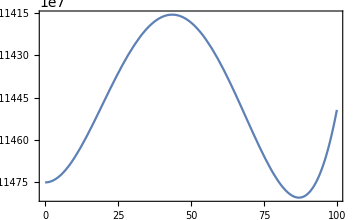

```mathematica
Plot[Vtotfull[ϕ,30,65.9],{ϕ,0,100}]
```

```mathematica
findThermo1loop[mh_]:=Block[{Tc,Tmax,Tmin,TT,Tm,Tp,Tloopmax,v1Limit,μhsq,g1sqInit,g2sqInit,g3sqInit,ytInit,μsqInit,λhInit,scale,g1sqvalue,g2sqvalue,g3sqvalue,ytvalue,μsqvalue,λhvalue,ng1sq,ng2sq,ng3sq,nyt,nμsq,nλ,g1sq3d,g2sq3d,g3sq3d,μhsq3d,λh3d,ϕ3,Veff,Veff0,Veffnorm,acc,scalingFactor,minSol,Tnext,Vc,ϕ0,ϕ3d,ϕc,ϕcTc,ϕ,Tupper},
Tmax=150;
Tmin=40;
Tloopmax=10;
v1Limit=40;
acc=10;
ϕ0=10^-5;
Tupper=Catch[Do[
Veff0=Vtotfull[ϕ0,mh,TT];
minSol=NMinimize[{Vtotfull[ϕ,mh,TT],ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>Veff0,Throw[TT];];
,{TT,Tmin,Tmax,10}]];
Tm=Tupper-10;
Tp=Tupper;
TT=(Tm+Tp)/2;
(*Scan over temeperatures*)
Do[
Veff0=Vtotfull[ϕ0,mh,TT];
minSol=NMinimize[{Vtotfull[ϕ,mh,TT],ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
If[Vc>Veff0,
Tnext=(TT+Tm)/2//N;
Tp=TT;
TT=Tnext;];
If[Vc<Veff0,
Tnext=(TT+Tp)/2//N;
Tm=TT;
TT=Tnext;];
If[Tloop==Tloopmax &&Vc>0,
(*In this case we cannot find the correct ϕc. Go back to the previous Tm.*)
Tc=Tm;
TT=Tc;
Veff0=Vtotfull[ϕ0,mh,TT];
minSol=NMinimize[{Vtotfull[ϕ,mh,TT],ϕ>v1Limit},{ϕ,1,500},Method->{"DifferentialEvolution","SearchPoints"->acc,"ScalingFactor"->0.6}];
Vc=minSol[[1]];
ϕc=minSol[[2]];
ϕcTc=ϕc/Tc;];
If[Tloop==Tloopmax &&Vc<0,
ϕc=Abs[ϕ]/.minSol[[2]];
Tc=TT//N;
ϕcTc=ϕc/Tc;];
,{Tloop,1,Tloopmax,1}
];
Print["Find critical temperature: ",Tc,", field value at vev: ",ϕc,", transition strength: ",ϕcTc," Veff at ϕc: ",Vc];
Return[{Tc,ϕc,ϕcTc}];
]
```

```mathematica
findThermo1loop[30]
```

Find critical temperature: 65.9131, field value at vev: 86.6109, transition strength: 1.31402 Veff at ϕc: -4.11681×10^7

{65.9131,86.6109,1.31402}

```mathematica
strength1looplist={};
Tc1looplist={};
Block[{mhrun,Tc,ϕc,ϕcTc},
Do[
mhrun=mh;
Print["Higgs mass: ",mhrun," GeV."];
{Tc,ϕc,ϕcTc}=findThermo1loop[mh];
AppendTo[Tc1looplist,{mhrun,Tc}];
AppendTo[strength1looplist,{mhrun,ϕcTc}];
,{mh,24,50,2}]]
```

Higgs mass: 24 GeV.

Find critical temperature: 54.9072, field value at vev: 105.911, transition strength: 1.92891 Veff at ϕc: -1.98365×10^7

Higgs mass: 26 GeV.

Find critical temperature: 58.5205, field value at vev: 99.0619, transition strength: 1.69277 Veff at ϕc: -2.55963×10^7

Higgs mass: 28 GeV.

Find critical temperature: 62.1924, field value at vev: 92.4393, transition strength: 1.48634 Veff at ϕc: -3.26501×10^7

Higgs mass: 30 GeV.

Find critical temperature: 65.9131, field value at vev: 86.6109, transition strength: 1.31402 Veff at ϕc: -4.11681×10^7

Higgs mass: 32 GeV.

Find critical temperature: 69.6631, field value at vev: 81.2891, transition strength: 1.16689 Veff at ϕc: -5.13682×10^7

Higgs mass: 34 GeV.

Find critical temperature: 73.4521, field value at vev: 76.1875, transition strength: 1.03724 Veff at ϕc: -6.34902×10^7

Higgs mass: 36 GeV.

Find critical temperature: 77.2705, field value at vev: 71.0162, transition strength: 0.91906 Veff at ϕc: -7.77976×10^7

Higgs mass: 38 GeV.

Find critical temperature: 81.1182, field value at vev: 66.5032, transition strength: 0.819831 Veff at ϕc: -9.44883×10^7

Higgs mass: 40 GeV.

Find critical temperature: 84.9854, field value at vev: 62.4726, transition strength: 0.735098 Veff at ϕc: -1.13836×10^8

Higgs mass: 42 GeV.

Find critical temperature: 88.8721, field value at vev: 58.7536, transition strength: 0.661103 Veff at ϕc: -1.36132×10^8

Higgs mass: 44 GeV.

Find critical temperature: 92.7881, field value at vev: 55.1844, transition strength: 0.594735 Veff at ϕc: -1.61689×10^8

Higgs mass: 46 GeV.

Find critical temperature: 96.7041, field value at vev: 51.603, transition strength: 0.533617 Veff at ϕc: -1.9084×10^8

Higgs mass: 48 GeV.

Find critical temperature: 100.649, field value at vev: 47.8193, transition strength: 0.475108 Veff at ϕc: -2.2394×10^8

Higgs mass: 50 GeV.

Find critical temperature: 104.604, field value at vev: 45.1226, transition strength: 0.431364 Veff at ϕc: -2.61169×10^8

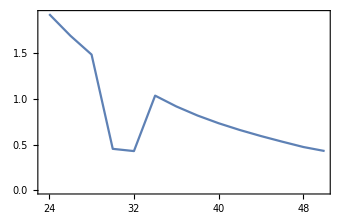

```mathematica
ListLinePlot[strength1looplist]
```

### High-T form with log term, resummation performed by 2E/3

```mathematica
DD=1/(8 v^2)(2 mW^2+mZ^2+2 mt^2);
EE=2/3 1/(4π v^3)(2 mW^3+mZ^3);
T0sqlog[mh_]:=1/(2DD)(μ[mh]^2-4B v^2);
aB=Exp[2Log[4π]-2EulerGamma];
aF=Exp[2Log[π]-2EulerGamma];
λT[mh_,T_]:=λ[mh]-3/(16 π^2 v^4)(2 mW^4 Log[mW^2/(aB T^2)]+mZ^4 Log[mZ^2/(aB T^2)]-4 mt^4 Log[mt^2/(aF T^2)]);
VhighTlog[ϕ_,mh_,T_]:=DD (T^2-T0sqlog[mh])ϕ^2-EE T ϕ^3+λT[mh,T]/4 ϕ^4;
```

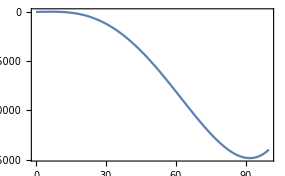

```mathematica
Plot[VhighTlog[ϕ,30,60.2356],{ϕ,0,100}]
```

```mathematica
FindRoot[x^2==T0sqlog[30]/(1-EE^2/(λT[30,x] DD)),{x,62}]
```

{x→61.0754}

```mathematica
strength1loophighTlog={};
Tc1loophighTlog={};
Block[{mhrun,Tc,ϕc,ϕcTc},
Do[
mhrun=mh;
Print["Higgs mass: ",mhrun," GeV."];
Tc=x/.FindRoot[x^2==T0sqlog[mhrun]/(1-EE^2/(λT[mhrun,x] DD)),{x,60}];
ϕc=2EE Tc/λT[mhrun,Tc];
ϕcTc=(2EE)/λT[mhrun,Tc];
AppendTo[Tc1loophighTlog,{mhrun,Tc}];
AppendTo[strength1loophighTlog,{mhrun,ϕcTc}];
,{mh,24,50,2}]]
```

Higgs mass: 24 GeV.

Higgs mass: 26 GeV.

Higgs mass: 28 GeV.

Higgs mass: 30 GeV.

Higgs mass: 32 GeV.

Higgs mass: 34 GeV.

Higgs mass: 36 GeV.

Higgs mass: 38 GeV.

Higgs mass: 40 GeV.

Higgs mass: 42 GeV.

Higgs mass: 44 GeV.

Higgs mass: 46 GeV.

Higgs mass: 48 GeV.

Higgs mass: 50 GeV.

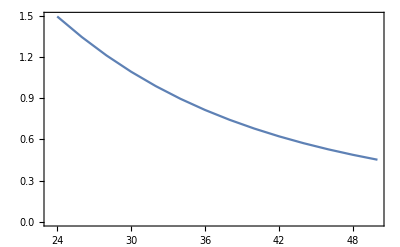

```mathematica
ListLinePlot[strength1loophighTlog]
```

### High-T form without log term, resummation performed by 2E/3

```mathematica
T0sq[mh_]:=1/(2DD)(μ[mh]^2);
VhighT[ϕ_,mh_,T_]:=DD(T^2-T0sq[mh])ϕ^2-EE T ϕ^3+λ[mh]/4 ϕ^4;
strengthhighT[mh_]:=2 EE/λ[mh];
```

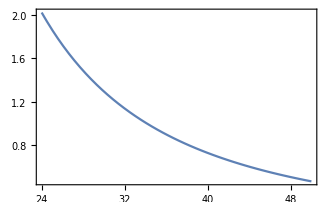

```mathematica
Plot[strengthhighT[mh],{mh,24,50}]
```

## Summary plot

```mathematica
strengthDR1loopfunc[mh_]=Interpolation[strengthlistDR1loop][mh];
strengthDR2loopfunc[mh_]=Interpolation[strengthlistDR2loop][mh];
strength4d1loopfunc[mh_]=Interpolation[strength1looplist][mh];
strength4dhighTlogfunc[mh_]=Interpolation[strength1loophighTlog][mh];
```

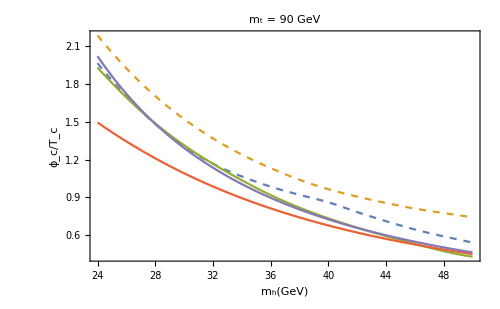

```mathematica
Plot[{strengthDR1loopfunc[mh],strengthDR2loopfunc[mh],strength4d1loopfunc[mh],strength4dhighTlogfunc[mh],strengthhighT[mh]},{mh,24,50},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_h(GeV)",FontFamily->"Times",FontSize->18],Style["ϕ_c/T_c",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->18],PlotRangePadding->None,ImageSize->500,PlotStyle->{Directive[Dashed,ColorData[97,1]],Directive[Dashed,ColorData[97,2]],ColorData[97,3],ColorData[97,4],ColorData[97,5]},PlotLabel->Style["m_t = 90 GeV",FontFamily->"Times",FontSize->24],Epilog->{Inset[Framed[Column[{LineLegend[{Directive[ColorData[97,1],Dashed],Directive[ColorData[97,2],Dashed],ColorData[97,3],ColorData[97,4],ColorData[97,5]},{Style["3d, 1-loop",FontFamily->"Times"],Style["3d, 2-loop",FontFamily->"Times"],Style["4d, Eq 49-50",FontFamily->"Times"],Style["4d, Eq 51-52",FontFamily->"Times"],Style["4d, Eq 53",FontFamily->"Times"]}]}],RoundingRadius->5],Scaled[{0.78,0.69}]]}]
```